## ZrC density of states and Einstein thermodynamic analysis;

QH Einstein approximation best with mean, mode, Einstein displacement or Trace of force constant matrix?
Variationally optimise the QH DOS via Gibbs-Bogoliubov

```mathematica
Some basic information;
aLabel={"4.575","4.600","4.625","4.6583","4.685","4.730","4.759","4.801","4.850"};
ePeRF={-673.82051,-674.79111,-675.40188,-675.68572,-675.50095,-674.41442,-673.23280,-670.90290,-667.33277};
eFren={-669.60769,-670.75114,-671.53884,-672.06424,-672.07754,-671.33314,-670.37803,-668.38638,-665.23097};
eCvac={-662.57856,-663.53617,-664.14458,-664.44074,-664.27725,-663.24766,-662.11597,-659.87660,-656.43966};
eZvac={-655.35351,-656.24549,-656.79543,-657.02389,-656.81424,-655.72117,-654.55722,-652.28142,-648.81500};
ePerfat=1000*ePeRF/64;eFrenat=1000*eFren/64;eCvacat=1000*eCvac/63;eZvacat=1000*eZvac/63;
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
m={12.0107,91.224,1};
```

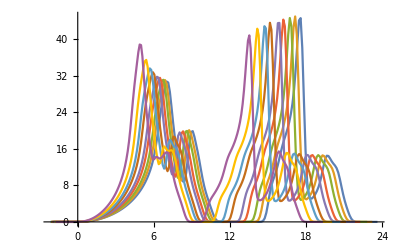

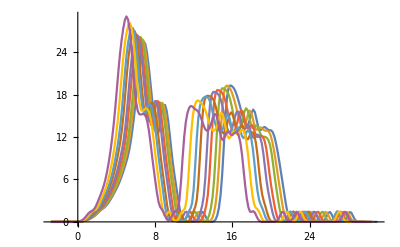

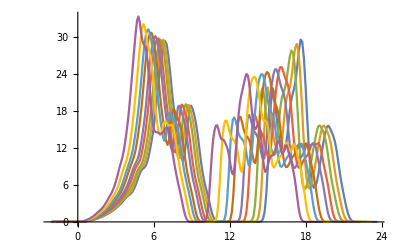

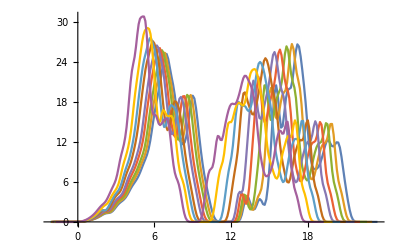

```mathematica
Import data;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/PERF_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllPERF=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
ListLinePlot@dosAllPERF
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/FREN_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllFREN=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
ListLinePlot@dosAllFREN
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/CVAC_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllCVAC=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
ListLinePlot@dosAllCVAC
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/ZVAC_qha700666_out/"];
file={"4.575a.total_dos.dat", "4.600a.total_dos.dat", "4.625a.total_dos.dat", "4.65837a.total_dos.dat", "4.685a.total_dos.dat", "4.730a.total_dos.dat", "4.759a.total_dos.dat", "4.801a.total_dos.dat", "4.850a.total_dos.dat"};
dosAllZVAC=Table[ReadList[file[[i]],{Number, Number}],{i,1,9}];
ListLinePlot@dosAllZVAC
```

```mathematica
Fit DOS using Mathematica interpolation routines;
PERFdosFITs=Table[Interpolation[dosAllPERF[[i]]],{i,1,9}];
FRENdosFITs=Table[Interpolation[dosAllFREN[[i]]],{i,1,9}];
CVACdosFITs=Table[Interpolation[dosAllCVAC[[i]]],{i,1,9}];
ZVACdosFITs=Table[Interpolation[dosAllZVAC[[i]]],{i,1,9}];
```

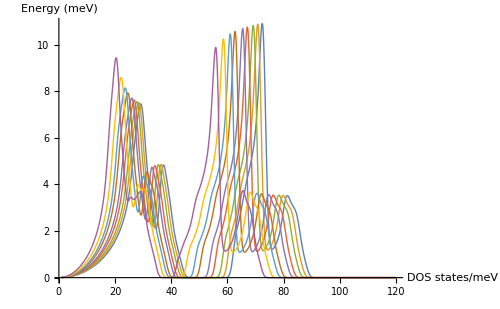

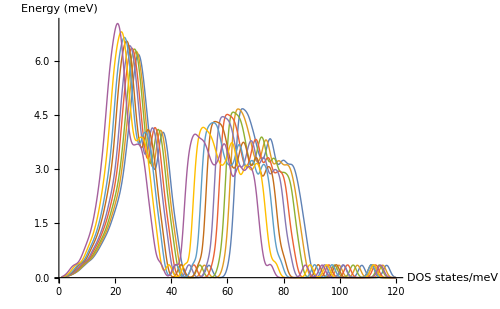

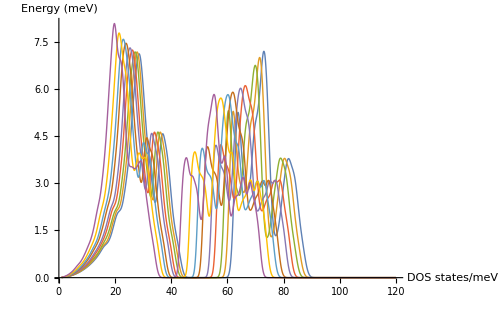

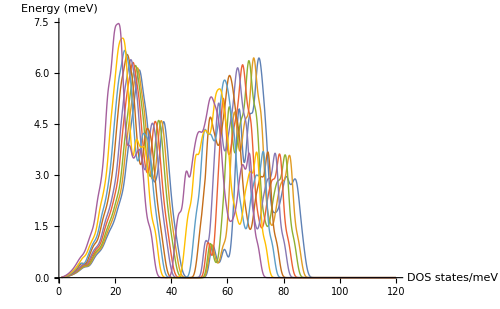

```mathematica
Plot interpolated DOS in meV ;
Plot[Evaluate@Table[THz2meV*PERFdosFITs[[i]][x*THz2meV],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}]
Plot[Evaluate@Table[THz2meV*FRENdosFITs[[i]][x*THz2meV],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}]
Plot[Evaluate@Table[THz2meV*CVACdosFITs[[i]][x*THz2meV],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}]
Plot[Evaluate@Table[THz2meV*ZVACdosFITs[[i]][x*THz2meV],{i,1,9}],{x,1,120},PlotLegends->SwatchLegend[labeldos],PlotStyle->Thick,ImageSize->500,AxesLabel->{"DOS\n states/meV","Energy (meV)"}]
```

```mathematica
Check number of modes;
Emin=0;Emax=120;
192 modes;
Table[NIntegrate[(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],{energy,Emin,Emax}],{i,1,9}]
Table[NIntegrate[(THz2meV)*FRENdosFITs[[i]][energy*THz2meV],{energy,Emin,Emax}],{i,1,9}]
189 modes;
Table[NIntegrate[(THz2meV)*ZVACdosFITs[[i]][energy*THz2meV],{energy,Emin,Emax}],{i,1,9}]
Table[NIntegrate[(THz2meV)*CVACdosFITs[[i]][energy*THz2meV],{energy,Emin,Emax}],{i,1,9}]
```

{191.999,191.999,191.999,191.999,191.999,191.999,191.999,191.999,191.999}

{191.996,191.998,191.998,191.998,191.998,191.998,191.998,191.997,191.995}

{188.999,188.999,188.999,188.999,188.999,188.999,188.999,188.999,188.999}

{188.999,188.999,188.999,188.999,188.999,188.999,188.999,188.999,188.999}

```mathematica
Get lower and upper band centres for PERF;
Off[NIntegrate::izero]
Off[NIntegrate::nlim]
Off[FindMaximum::cvmit]
(*Get the lower band centres - median and mode*)
(*Excuse the hacky way to extract peaks maxima in phonon DOS*)
"Lower PERF mode:"
lowerPERFmode=Table[FindMaximum[{(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],0<energy<31-i},energy][[2]][[1]][[2]],{i,1,9}]
"Lower PERF median:"
lowerPERFmedian=Table[medianLowerBand/.FindRoot[NIntegrate[(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],{energy,0,medianLowerBand}]-48==0,{medianLowerBand,1}],{i,1,9}]
(*Extract a mid point where the DOS goes to zero*)
"PERF DOS zero midpoints:"
midpointPERF=
Table[FindMinimum[{(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],energy>40},energy][[2]][[1]][[2]],{i,1,9}]
(*Get the upper band centres - median and mode*)
Off[InterpolatingFunction::dmval]
Off[General::stop]
"Upper PERF mode:"
upperPERFmode=Table[FindMaximum[{(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],energy>62-2.2*i},energy][[2]][[1]][[2]],{i,1,9}]
"Upper PERF median:"
upperPERFmedian=
Table[medianUpperBand/.FindRoot[NIntegrate[(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],{energy,midpointPERF[[i]],medianUpperBand}]-48==0,{medianUpperBand,60}],{i,1,9}]
```

Lower PERF mode:

{29.1337,28.43,27.7414,26.7766,25.963,24.5468,23.6067,22.1858,20.3726}

Lower PERF median:

{29.5568,28.8407,28.1188,27.1387,26.3401,24.9507,24.026,22.6324,20.9013}

PERF DOS zero midpoints:

{54.6977,52.5735,45.4039,44.2896,43.4227,41.6064,41.069,41.0759,40.}

Upper PERF mode:

{72.3864,70.7944,69.1689,67.0743,65.4438,62.7025,60.9981,58.563,55.8259}

Upper PERF median:

{72.1926,70.5744,68.9623,66.8316,65.1587,62.3896,60.6454,58.179,55.3851}

```mathematica
Define arithmetic and geometric means;
GM[arg_,space_,max_,min_]:=Exp[Integrate[Log[arg]*space,{energy,min,max}]/Integrate[space,{energy,min,max}]]//N
AM[arg_,space_,max_,min_]:=Integrate[arg*space,{energy,min,max}]/Integrate[space,{energy,min,max}]//N
HM[arg_,space_,max_,min_]:=(Integrate[space,{energy,min,max}]/Integrate[space/arg,{energy,min,max}])//N
```

```mathematica
PERFdosFITs//Length
```

9

#### Extract perfect GMs

```mathematica
lowerZrGM=Table[GM[energy,(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],62-2.2*i,0],{i,1,9}]
upperCGM=Table[GM[energy,(THz2meV)*PERFdosFITs[[i]][energy*THz2meV],62-2.2*i,120],{i,1,9}]
```

{28.6036,27.932,27.251,26.326,25.5759,24.2808,23.4255,22.1562,20.6676}

{73.1844,71.5584,69.9256,67.7521,66.0392,63.1982,61.4047,58.8719,56.0685}

## Convert GMs to Hessian TI units

```mathematica
Units;
(*1 Bohr=0.529177208 Angstrom*)
(*1Hartree=27.211396 eV*)
ang2bohr=1/0.529177208;
ev2har=1/27.211396;
```

```mathematica
Convert the Hessian diagonals to Einstein frequencies;
hessToEinZr[arg_]:=2Sqrt[arg/HarBohr/mass[[1]]]
hessToEinC[arg_]:=2Sqrt[arg/HarBohr/mass[[2]]]
EinToHessC[arg_]:=((arg/2)^2)*HarBohr*mass[[2]]
EinToHessZr[arg_]:=((arg/2)^2)*HarBohr*mass[[1]]
```

```mathematica
EinToHessC[upperCGM]
EinToHessZr[lowerZrGM]
```

{0.165499,0.158227,0.151089,0.141842,0.134761,0.123415,0.11651,0.107097,0.0971397}

{0.192018,0.183107,0.174287,0.162656,0.153519,0.138365,0.128789,0.115211,0.10025}

```mathematica
alatts
```

{4.575,4.6,4.625,4.6583,4.685,4.73,4.759,4.801,4.85}

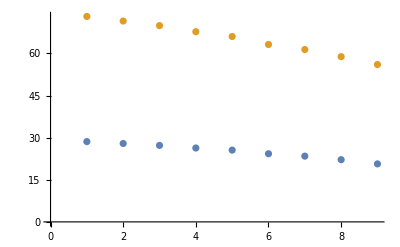

```mathematica
ListPlot[{lowerZrGM,upperCGM}]
```

#### Extract the C Gruneisen to Zr Gruneisen ratio

```mathematica
Transpose@{alatts^3,lowerZrGM}
```

{{95.7576,28.6036},{97.336,27.932},{98.9316,27.251},{101.084,26.326},{102.832,25.5759},{105.824,24.2808},{107.782,23.4255},{110.661,22.1562},{114.084,20.6676}}

```mathematica
Log[alatts[[1]]^3]
Log[alatts[[-1]]^3]
Log@94//N
Log@115//N
```

4.56182

4.73694

4.54329

4.74493

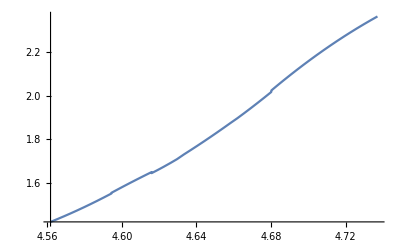

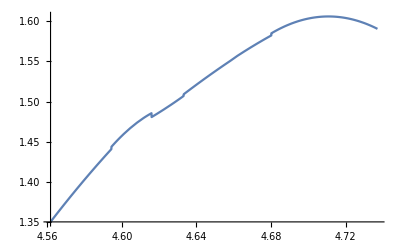

```mathematica
interLowerGMlog=Interpolation[Transpose@{Log[alatts^3],Log@lowerZrGM}];
interUpperGMlog=Interpolation[Transpose@{Log[alatts^3],Log@upperCGM}];
Plot[Evaluate[-D[interLowerGMlog[V],V]],{V,Log[alatts[[1]]^3],Log[alatts[[-1]]^3]}]
Plot[Evaluate[-D[interUpperGMlog[V],V]],{V,Log[alatts[[1]]^3],Log[alatts[[-1]]^3]}]
```

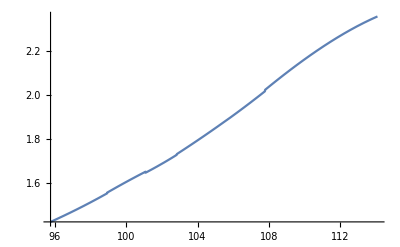

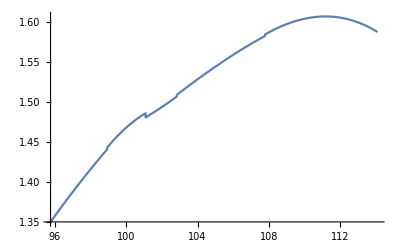

(InterpolatingFunction[{{95.7576, 114.084}}, <>][V] InterpolatingFunction[{{95.7576, 114.084}}, <>][V])/(InterpolatingFunction[{{95.7576, 114.084}}, <>][V] InterpolatingFunction[{{95.7576, 114.084}}, <>][V])

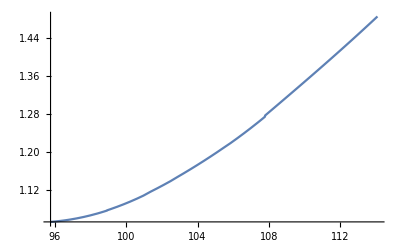

```mathematica
interLowerGMlog2=Interpolation[Transpose@{alatts^3,lowerZrGM}];
interUpperGMlog2=Interpolation[Transpose@{alatts^3,upperCGM}];
Plot[Evaluate[-(V/interLowerGMlog2[V])*D[interLowerGMlog2[V],V]],{V,alatts[[1]]^3,alatts[[-1]]^3}]
Plot[Evaluate[-(V/interUpperGMlog2[V])*D[interUpperGMlog2[V],V]],{V,alatts[[1]]^3,alatts[[-1]]^3}]
(*Look at the Gruneisen ratios for Zr and C*)

ZoverCgrun=(Evaluate[-(V/interLowerGMlog2[V])*D[interLowerGMlog2[V],V]])/(Evaluate[-(V/interUpperGMlog2[V])*D[interUpperGMlog2[V],V]])
Plot[ZoverCgrun,{V,alatts[[1]]^3,alatts[[-1]]^3}]
```

```mathematica
Get lower and upper band centres for FREN;
Off[NIntegrate::izero]
Off[NIntegrate::nlim]
Off[FindMaximum::cvmit]
(*Get the lower band centres-median and mode*)
(*Excuse the hacky way to extract peaks maxima in phonon DOS*)
"Lower FREN mode:"
lowerFRENmode=Table[FindMaximum[{(THz2meV)*FRENdosFITs[[i]][energy*THz2meV],0<energy<31-i},energy][[2]][[1]][[2]],{i,1,9}]
"Lower FREN median:"
lowerFRENmedian=Table[medianLowerBand/.FindRoot[NIntegrate[(THz2meV)*FRENdosFITs[[i]][energy*THz2meV],{energy,0,medianLowerBand}]-48==0,{medianLowerBand,1}],{i,1,9}]
(*Extract a mid point where the DOS goes to zero - serves as a point within to define the separation of Zr species and C species phonon DOS bands*)
"FREN DOS zero midpoints:"
midpointFREN=Table[FindMinimum[{(THz2meV)*FRENdosFITs[[i]][energy*THz2meV],energy>40},energy][[2]][[1]][[2]],{i,1,9}]
(*Get the upper band centres-median and mode*)Off[InterpolatingFunction::dmval]
Off[General::stop]
"Upper FREN mode:"
upperFRENmode=Table[FindMaximum[{(THz2meV)*FRENdosFITs[[i]][energy*THz2meV],energy>65-2*i},energy][[2]][[1]][[2]],{i,1,9}]
"Upper FREN median:"
upperFRENmedian=Table[medianUpperBand/.FindRoot[NIntegrate[(THz2meV)*FRENdosFITs[[i]][energy*THz2meV],{energy,midpoint[[i]],medianUpperBand}]-48==0,{medianUpperBand,65}],{i,1,9}]
```

Lower FREN mode:

{28.2845,27.592,26.9193,25.9572,25.2562,24.1121,23.3411,22.2534,20.8886}

Lower FREN median:

{29.1168,28.439,27.7645,26.8569,26.1286,24.8881,24.0742,22.8736,21.4156}

FREN DOS zero midpoints:

{57.2514,46.9701,45.7501,44.0137,42.8114,40.6328,40.,42.0306,40.}

Upper FREN mode:

{65.2934,63.7811,62.0742,59.9736,58.3282,55.5801,54.9151,51.3856,48.5104}

Upper FREN median:

Part::partd: Part specification midpoint⟦1⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦3⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦4⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦5⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦6⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦7⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦8⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦9⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]}

```mathematica
Get lower and upper band centres for CVAC;
Off[NIntegrate::izero]
Off[NIntegrate::nlim]
Off[FindMaximum::cvmit]
(*Get the lower band centres-median and mode*)
(*Excuse the hacky way to extract peaks maxima in phonon DOS*)
"Lower CVAC mode:"
lowerCVACmode=Table[FindMaximum[{(THz2meV)*CVACdosFITs[[i]][energy*THz2meV],0<energy<31-i},energy][[2]][[1]][[2]],{i,1,9}]
"Lower CVAC median:"
lowerCVACmedian=Table[medianLowerBand/.FindRoot[NIntegrate[(THz2meV)*CVACdosFITs[[i]][energy*THz2meV],{energy,0,medianLowerBand}]-48==0,{medianLowerBand,1}],{i,1,9}]
(*Extract a mid point where the DOS goes to zero*)
"CVAC DOS zero midpoints:"
midpointCVAC=Table[FindMinimum[{(THz2meV)*CVACdosFITs[[i]][energy*THz2meV],energy>40},energy][[2]][[1]][[2]],{i,1,9}]
(*Get the upper band centres-median and mode*)Off[InterpolatingFunction::dmval]
Off[General::stop]
"Upper CVAC mode:"
upperCVACmode=Table[FindMaximum[{(THz2meV)*CVACdosFITs[[i]][energy*THz2meV],energy>72-2*i},energy][[2]][[1]][[2]],{i,1,9}]
"Upper CVAC median:"
upperCVACmedian=Table[medianUpperBand/.FindRoot[NIntegrate[(THz2meV)*CVACdosFITs[[i]][energy*THz2meV],{energy,midpoint[[i]],medianUpperBand}]-48==0,{medianUpperBand,65}],{i,1,9}]
```

Lower CVAC mode:

{28.5348,27.8576,27.1314,26.1513,25.3422,23.9092,22.9423,21.4471,19.7823}

Lower CVAC median:

{29.254,28.5605,27.8696,26.9351,26.1823,24.8857,24.0303,22.7674,21.2032}

CVAC DOS zero midpoints:

{47.0732,49.122,45.0056,43.9147,43.0615,41.6409,41.1608,41.0989,40.3941}

Upper CVAC mode:

{72.9751,71.4762,69.903,66.3628,64.6822,61.9107,60.1676,57.6468,55.2298}

Upper CVAC median:

Part::partd: Part specification midpoint⟦1⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦3⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦4⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦5⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦6⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦7⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦8⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦9⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV CVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]}

```mathematica
Get lower and upper band centres for ZVAC;
Off[NIntegrate::izero]
Off[NIntegrate::nlim]
Off[FindMaximum::cvmit]
(*Get the lower band centres-median and mode*)
(*Excuse the hacky way to extract peaks maxima in phonon DOS*)
"Lower ZVAC mode:"
lowerZVACmode=Table[FindMaximum[{(THz2meV)*ZVACdosFITs[[i]][energy*THz2meV],0<energy<31-i},energy][[2]][[1]][[2]],{i,1,9}]
"Lower ZVAC median:"
lowerZVACmedian=Table[medianLowerBand/.FindRoot[NIntegrate[(THz2meV)*ZVACdosFITs[[i]][energy*THz2meV],{energy,0,medianLowerBand}]-48==0,{medianLowerBand,1}],{i,1,9}]
(*Extract a mid point where the DOS goes to zero*)
"ZVAC DOS zero midpoints:"
midpointZVAC=Table[FindMinimum[{(THz2meV)*ZVACdosFITs[[i]][energy*THz2meV],energy>40},energy][[2]][[1]][[2]],{i,1,9}]
(*Get the upper band centres-median and mode*)Off[InterpolatingFunction::dmval]
Off[General::stop]
"Upper ZVAC mode:"
upperZVACmode=Table[FindMaximum[{(THz2meV)*ZVACdosFITs[[i]][energy*THz2meV],energy>72-2*i},energy][[2]][[1]][[2]],{i,1,9}]
"Upper ZVAC median:"
upperZVACmedian=Table[medianUpperBand/.FindRoot[NIntegrate[(THz2meV)*ZVACdosFITs[[i]][energy*THz2meV],{energy,midpoint[[i]],medianUpperBand}]-48==0,{medianUpperBand,65}],{i,1,9}]
```

Lower ZVAC mode:

{28.639,27.9623,27.2577,26.3886,25.6068,24.3171,23.4468,22.7011,21.2277}

Lower ZVAC median:

{29.5958,28.8997,28.2011,27.2596,26.4982,25.1842,24.308,22.9965,21.3514}

ZVAC DOS zero midpoints:

{47.6662,46.3693,45.5185,44.0033,43.1205,41.7133,41.2342,40.8099,40.}

Upper ZVAC mode:

{71.2146,69.342,67.6285,65.4187,63.653,60.7447,59.0001,57.1753,54.2157}

Upper ZVAC median:

Part::partd: Part specification midpoint⟦1⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦2⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦3⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦4⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦5⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦6⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦7⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦8⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification midpoint⟦9⟧ is longer than depth of object.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::nlnum: The function value {-48.+NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]} is not a list of numbers with dimensions {1} at {medianUpperBand} = {65.}.

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}],medianUpperBand/.FindRoot[NIntegrate[THz2meV ZVACdosFITs⟦i⟧[energy THz2meV],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]}

```mathematica
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{#1,axisOrigin},{#1,#2}}&@@@a]};
horizontalListPlotFill[Evaluate@ListPlot[{Table[{upperPERFmedian[[i]],1},{i,1,9}],Table[{upperFRENmedian[[i]],1},{i,1,9}],Table[{upperCVACmedian[[i]],1},{i,1,9}],Table[{upperZVACmedian[[i]],1},{i,1,9}]}]]
```

ReplaceAll::reps: {FindRoot[NIntegrate[THz2meV FRENdosFITs⟦i⟧[Times[«2»]],{energy,midpoint⟦i⟧,medianUpperBand}]-48==0,{medianUpperBand,65}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted[]

#### Hessian diagonal elements 1 and 192

```mathematica
lowerPERFhess={0.227134990752235782,0.215629510044018896,0.204482192291760928,0.190171820406654507,0.179255218502894081,0.161823568215306995,0.151273943385760723,0.136865113734847693,0.121304891648369606};
upperPERFhess={0.158410899076719930,0.151742568391175114,0.145176379597923289,0.136639707968101709,0.130071877783300593,0.119478182362475024,0.112988572974945550,0.104053449687505489,0.0942772701666999002};
(*Note the Frenkel Hessian has to be resubmitted as rearranged!, and the Hessian Einstein constants extracted carefully taking into accuont defect position*)
lowerFRENhess={0.217730563262878152,0.206174806577149372,0.195055773242902186,0.180906947216968150,0.170066456484977313,0.152784347772913387,0.142247699712918563,0.127777716649587952E,0.111956137690552585};
upperFRENhess={0.159420416624561911,0.153008446600934017,0.146795537752417687,0.138830137272252602,0.132679318304059657,0.122799798006224523,0.116749314885077782,0.108444341880512066,0.994799102348783298};
(*tamellan@tycpc34:/workspace/tamellan/Tessa_ZrC/700_666/CVAC_REARRANGE/HesseMatrix_rearr*)
(*CVAC has 4 species, with Zr vac NN and C vac NN having two types of force constant with different degeneracies - for the time being only consider the normal sites in the CVAC crystal*)
(*lowerCVAChess={};upperCVAChess={};*)
lowerCVAChess={0.226439282570529726,0.214839223749259012,0.203702927503891823,0.189517249922237591,0.178723716366664315,0.161451898510707709,0.150953424381442936,0.136562397911595523,0.120953922000830133};
upperCVAChess={0.159958639714926965,0.156117018908149746,0.152352691571383175,0.147465455006159207,0.143695990295091086,0.137616067897763844,0.133936791029598351,0.129008164400599423,0.123981360074614633};
```

```mathematica
Convert the Hessian diagonals to Einstein frequencies;
hessToEinZr[arg_]:=2Sqrt[arg/HarBohr/mass[[1]]]
hessToEinC[arg_]:=2Sqrt[arg/HarBohr/mass[[2]]]
lowerPERFhessEin=hessToEinZr[lowerPERFhess]
upperPERFhessEin=hessToEinC[upperPERFhess]
lowerFRENhessEin=hessToEinZr[lowerFRENhess]
upperFRENhessEin=hessToEinC[upperFRENhess]
lowerCVAChessEin=hessToEinZr[lowerCVAChess]
upperCVAChessEin=hessToEinC[upperCVAChess]
```

{31.1094,30.3112,29.5174,28.4658,27.6367,26.2585,25.3882,24.1488,22.7347}

{71.5999,70.0767,68.5438,66.498,64.8801,62.182,60.4696,58.0294,55.2362}

{30.4586,29.6393,28.829,27.7637,26.919,25.5146,24.6191,38.4702,21.8411}

{71.8277,70.3684,68.925,67.0289,65.5272,63.0404,61.4677,59.2412,179.427}

{31.0617,30.2557,29.4611,28.4167,27.5957,26.2284,25.3613,24.1221,22.7018}

{71.9489,71.0796,70.2175,69.0821,68.1934,66.7352,65.837,64.6143,63.343}

```mathematica
ListPlot@lowerPERFhessEin;
ListPlot@upperPERFhessEin;
```

#### Einstein frequencies: 1) EinMedian - Extracted as the energy of the 48th mode (there are 96 modes per super-cell species) 2) EinMode - The frequency corresponding to the highest peak in each band of the DOS 3) EinHess - The frequency extract from the diagonal elements of the Hessian

```mathematica
(*These omega0s can be used to generate the vibrational excitation spectrums ie E=hbar*omega(n+0.5)*)
medianEin={Transpose@{lowerPERFmedian,upperPERFmedian},Transpose@{lowerFRENmedian,upperFRENmedian},Transpose@{lowerCVACmedian,upperCVACmedian},Transpose@{lowerZVACmedian,upperZVACmedian}};
modeEin={Transpose@{lowerPERFmode,upperPERFmode},Transpose@{lowerFRENmode,upperFRENmode},Transpose@{lowerCVACmode,upperCVACmode},Transpose@{lowerZVACmode,upperZVACmode}};
hessEin={Transpose@{lowerPERFhessEin,upperPERFhessEin},Transpose@{lowerFRENhessEin,upperFRENhessEin},Transpose@{lowerCVAChessEin,upperCVAChessEin}};
```

```mathematica
1) Easy method - Harmonic approximation heat capacity expression (phonopy website);
```

```mathematica
Cv[T_,freqs_,dosfactor_,freqfactor_]:=dosfactor*(K2meV*((((freqfactor*freqs))/(K2meV*T))^2)*Exp[((freqfactor*freqs))/(K2meV*T)]/((Exp[((freqfactor*freqs))/(K2meV*T)]-1)^2))
```

29.5568

72.1926

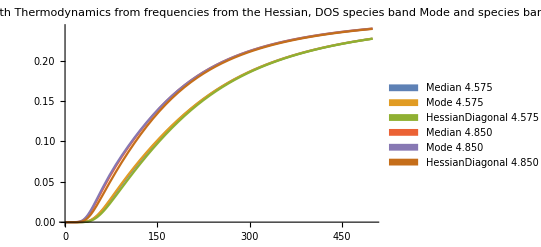

```mathematica
medianEin[[1]][[1]][[1]]
medianEin[[1]][[1]][[2]]
Plot[{Cv[T,medianEin[[1]][[1]][[1]],3/2,1]+Cv[T,medianEin[[1]][[1]][[2]],3/2,1],Cv[T,modeEin[[1]][[1]][[1]],3/2,1]+Cv[T,modeEin[[1]][[1]][[2]],3/2,1],Cv[T,hessEin[[1]][[1]][[1]],3/2,1]+Cv[T,hessEin[[1]][[1]][[2]],3/2,1],Cv[T,medianEin[[1]][[9]][[1]],3/2,1]+Cv[T,medianEin[[1]][[9]][[2]],3/2,1],Cv[T,modeEin[[1]][[9]][[1]],3/2,1]+Cv[T,modeEin[[1]][[9]][[2]],3/2,1],Cv[T,hessEin[[1]][[9]][[1]],3/2,1]+Cv[T,hessEin[[1]][[9]][[2]],3/2,1]},{T,1,500},PlotRange->All,PlotLabel->"Cv at 4.575Ang and 4.850Ang,\n with Thermodynamics from frequencies from the\n Hessian, DOS species band Mode and species band Median freqs",PlotLegends->SwatchLegend[{"Median 4.575","Mode 4.575","HessianDiagonal 4.575","Median 4.850","Mode 4.850","HessianDiagonal 4.850"}]]
```

```mathematica
2) General method  Heat Capacity via Free Energy from partition function;
```

```mathematica
(*Define free energy as log partition function and make excitation spectrum from the omega0 obtained from DOS median, mode, and Hessian*)
fr[T_,spectrumZ_,spectrumC_,maxEigen_,xFactor_,pFactor_]:=-K2meV*(pFactor)*T*Log[{Total[Exp[-xFactor*spectrumZ/(K2meV*T)]],Total[Exp[-xFactor*spectrumC/(K2meV*T)]]}]
maxval=200;
spectrumCmedian=Table[Table[medianEin[[1]][[k]][[2]]*(j-0.5),{j,1,maxval}],{k,1,9}];
spectrumZmedian=Table[Table[medianEin[[1]][[k]][[1]]*(j-0.5),{j,1,maxval}],{k,1,9}];
spectrumCmode=Table[Table[modeEin[[1]][[k]][[2]]*(j-0.5),{j,1,maxval}],{k,1,9}];
spectrumZmode=Table[Table[modeEin[[1]][[k]][[1]]*(j-0.5),{j,1,maxval}],{k,1,9}];
spectrumChess=Table[Table[hessEin[[1]][[k]][[2]]*(j-0.5),{j,1,maxval}],{k,1,9}];
spectrumZhess=Table[Table[hessEin[[1]][[k]][[1]]*(j-0.5),{j,1,maxval}],{k,1,9}];
```

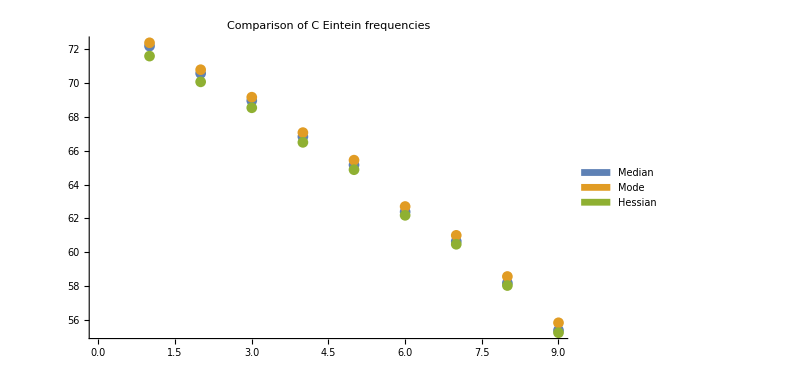

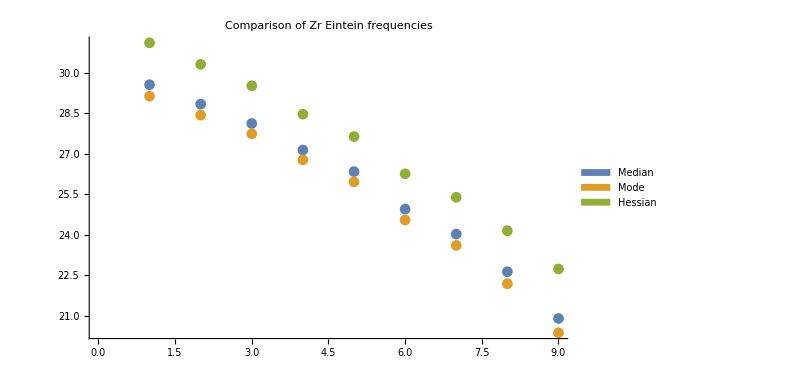

```mathematica
ListPlot[{Table[medianEin[[1]][[k]][[2]],{k,1,9}],Table[modeEin[[1]][[k]][[2]],{k,1,9}],Table[hessEin[[1]][[k]][[2]],{k,1,9}]},PlotLegends->SwatchLegend[{"Median","Mode","Hessian"}],PlotLabel->"Comparison of C Eintein frequencies",ImageSize->600]
ListPlot[{Table[medianEin[[1]][[k]][[1]],{k,1,9}],Table[modeEin[[1]][[k]][[1]],{k,1,9}],Table[hessEin[[1]][[k]][[1]],{k,1,9}]},PlotLegends->SwatchLegend[{"Median","Mode","Hessian"}],PlotLabel->"Comparison of Zr Eintein frequencies",ImageSize->600]
```

```mathematica
(*indicies*)
(*medianEin[[Crystal:PERF|FREN|CVAC]][[Volumes:1||9]][[Element:1|2]]*)
```

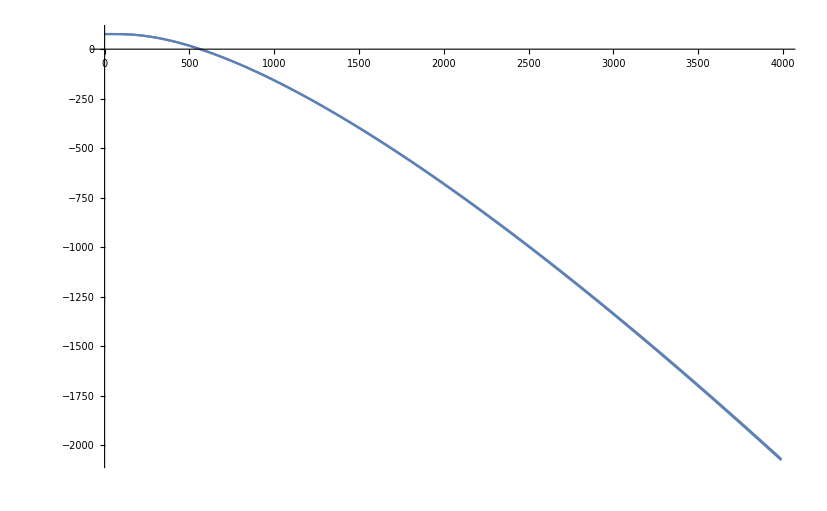

```mathematica
(*Free energy*)
minT=1;maxT=4000;dT=10;
Show[ListLinePlot[Table[Table[{t,Total@fr[t,spectrumCmedian[[k]],spectrumZmedian[[k]],70,1,1.5]},{t,minT,maxT,dT}],{k,1,1}]],ListLinePlot[Table[Table[{t,Total@fr[t,spectrumCmode[[k]],spectrumZmode[[k]],70,1,1.5]},{t,minT,maxT,dT}],{k,1,1}]]]
```

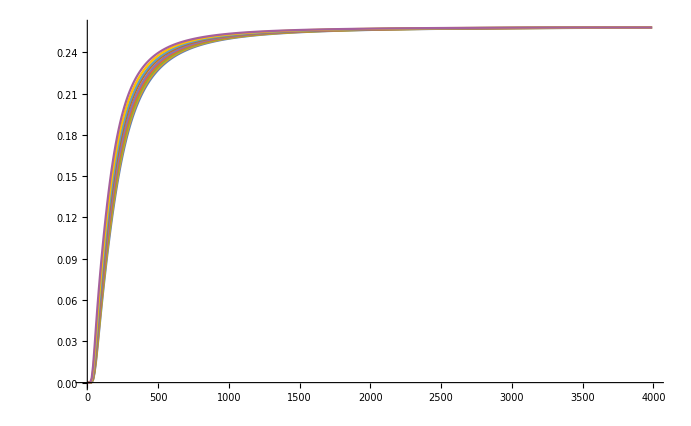

```mathematica
(*Heat capacity*)
ListLinePlot[Table[Table[{T,t*D[-D[Total@fr[t,spectrumC[[k]],spectrumZ[[k]],150,1,1.5],t],t]}/.t->T,{T,minT,maxT,dT}],{k,1,9}],PlotRange->All]
```

#### E0 Volume dependence at zero temperature excluding ZP effects;

```mathematica
(*Perf*)
eafitPerf=Fit[Transpose[{alatts,ePerfat}],{1,x,x*x,x*x*x},x]
eafitMinPerf=FindMinimum[Evaluate@eafitPerf,x][[1]]
e0Perf=ePerfat[[1;;9]]-eafitMinPerf




(*Fren and Cvac*)
eafitFren=Fit[Transpose[{alatts,eFrenat}],{1,x,x*x,x*x*x},x]
eafitMinFren=FindMinimum[Evaluate@eafitFren,x,PrecisionGoal->20][[1]]
e0Fren=eFrenat[[1;;9]]-eafitMinFren
eafitCvac=Fit[Transpose[{alatts,eCvacat}],{1,x,x*x,x*x*x},x]
eafitMinCvac=FindMinimum[Evaluate@eafitCvac,x,PrecisionGoal->20][[1]]
e0Cvac=eCvacat[[1;;9]]-eafitMinCvac
```

322945.-196102. x+38087.3 x^2-2438.45 x^3

-10557.6

{29.1486,13.983,4.43971,0.00471107,2.89174,19.8688,38.3316,74.7363,130.52}

326495.-198319. x+38581.1 x^2-2476.8 x^3

-10501.8

{39.1968,21.3304,9.02263,0.813252,0.60544,12.2367,27.1603,58.2798,107.583}

320417.-194679. x+37829.7 x^2-2423.57 x^3

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-10546.7

{29.5661,14.3659,4.70859,0.00764153,2.60272,18.9454,36.9088,72.4543,127.009}

#### Plot E0 vs volume;

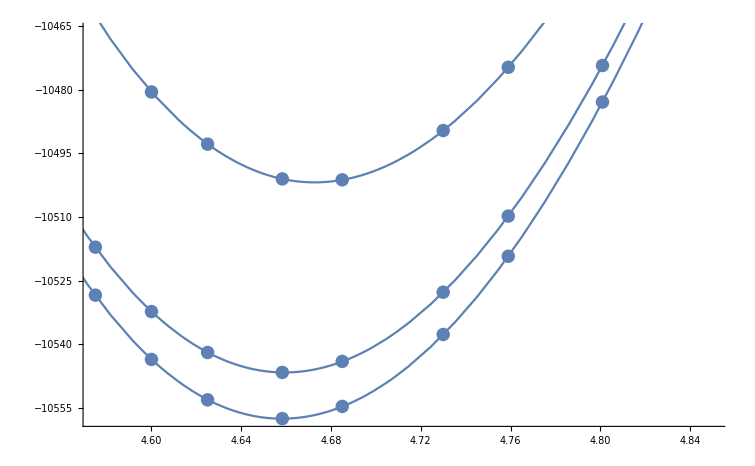

```mathematica
Show[{ListPlot[Transpose[{alatts,ePerfat}]],Plot[Evaluate@eafitPerf,{x,4.5,5}],
ListPlot[Transpose[{alatts,eFrenat}]],Plot[Evaluate@eafitFren,{x,4.5,5}],ListPlot[Transpose[{alatts,eCvacat}]],Plot[Evaluate@eafitCvac,{x,4.5,5}]}]
```

#### Helmholtz free F=E0(V)+Fvib(V,T) energies at volumes;

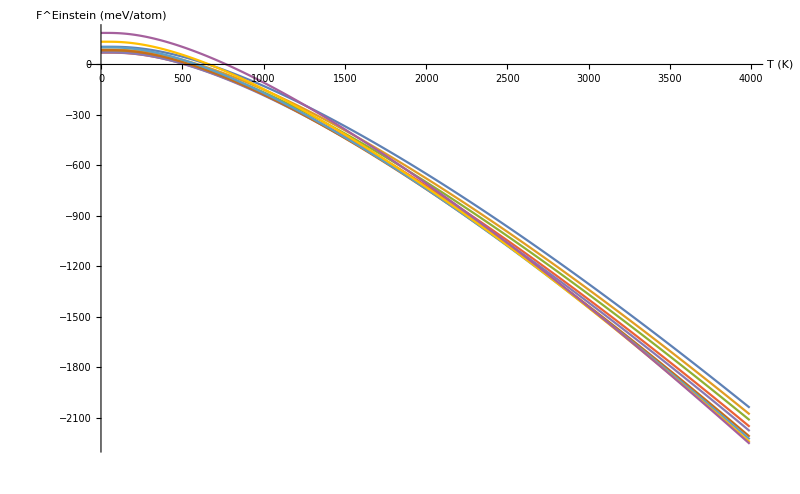

-Graphics-

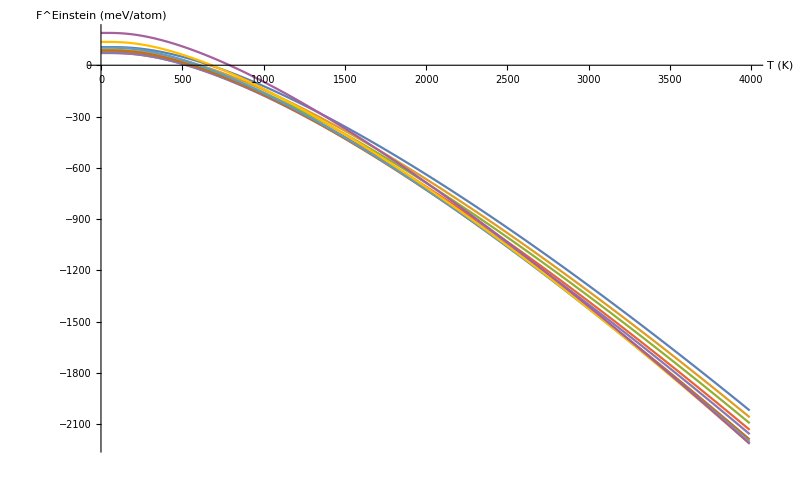

```mathematica
ListLinePlot[Table[Table[{t,e0Perf[[k]]+Total@fr[t,spectrumCmedian[[k]],spectrumZmedian[[k]],150,1,1.5]},{t,minT,maxT,dT}],{k,1,9}],PlotLegends->SwatchLegend[plab],ImageSize->800,AxesLabel->{"T (K)","F^Einstein (meV/atom)"},PlotStyle->PointSize[0.2]]
ListLinePlot[Table[Table[{t,e0Perf[[k]]+Total@fr[t,spectrumCmedian[[k]],spectrumZmedian[[k]],150,1,1.5]},{t,minT,maxT,dT}],{k,1,9}],PlotLegends->SwatchLegend[plab],ImageSize->800,AxesLabel->{"T (K)","F^Einstein (meV/atom)"},PlotStyle->PointSize[0.2]]
ListLinePlot[Table[Table[{t,e0Perf[[k]]+Total@fr[t,spectrumChess[[k]],spectrumZhess[[k]],150,1,1.5]},{t,minT,maxT,dT}],{k,1,9}],PlotLegends->SwatchLegend[plab],ImageSize->800,AxesLabel->{"T (K)","F^Einstein (meV/atom)"},PlotStyle->PointSize[0.2]]
```

#### Minimise the free energy in volume;

```mathematica
(*Make a list of temperatures at which to trial minimisation in V of F to generate G*)
temps[t_]:=1+9.6t^2
tlist=Table[temps[t],{t,0,22}]
(*Fit the F(T) in V at each to make F(V;T) for each chosen trial temperature - use a polynomial basis, with up to 3rd order terms*)
gfitPerfmode=Table[Fit[Table[{alatts[[k]],e0Perf[[k]]+Total@fr[t,spectrumCmode[[k]],spectrumZmode[[k]],150,1,1.5]},{k,1,9}]/.t->tlist[[j]],{1,x,x*x,x*x*x},x],{j,1,22}];
gfitPerfmedian=Table[Fit[Table[{alatts[[k]],e0Perf[[k]]+Total@fr[t,spectrumCmedian[[k]],spectrumZmedian[[k]],150,1,1.5]},{k,1,9}]/.t->tlist[[j]],{1,x,x*x,x*x*x},x],{j,1,22}];
gfitPerfhess=Table[Fit[Table[{alatts[[k]],e0Perf[[k]]+Total@fr[t,spectrumChess[[k]],spectrumZhess[[k]],150,1,1.5]},{k,1,9}]/.t->tlist[[j]],{1,x,x*x,x*x*x},x],{j,1,22}];
```

{1.,10.6,39.4,87.4,154.6,241.,346.6,471.4,615.4,778.6,961.,1162.6,1383.4,1623.4,1882.6,2161.,2458.6,2775.4,3111.4,3466.6,3841.,4234.6,4647.4}

```mathematica
Extract minimum lattice parameters and Gibbs energy at each T;
(*mode*)
minPerfmode=Table[Minimize[{gfitPerfmode[[i]],4.575<x<5},x],{i,1,22}];
minAPerfmode=Table[minPerfmode[[i]][[2]][[1]][[2]],{i,1,22}]
mine0Perfmode=Table[minPerfmode[[i]][[1]],{i,1,22}]
(*median*)
minPerfmedian=Table[Minimize[{gfitPerfmedian[[i]],4.575<x<5},x],{i,1,22}];
minAPerfmedian=Table[minPerfmedian[[i]][[2]][[1]][[2]],{i,1,22}]
mine0Perfmedian=Table[minPerfmedian[[i]][[1]],{i,1,22}]
(*hessian*)
minPerfhess=Table[Minimize[{gfitPerfhess[[i]],4.575<x<5},x],{i,1,22}];
minAPerfhess=Table[minPerfhess[[i]][[2]][[1]][[2]],{i,1,22}]
mine0Perfhess=Table[minPerfhess[[i]][[1]],{i,1,22}]
```

{4.66676,4.66676,4.66676,4.66693,4.66773,4.66946,4.67222,4.67598,4.68071,4.68641,4.69312,4.70092,4.70994,4.72036,4.73245,4.74662,4.76349,4.78415,4.81074,4.84892,5.,5.}

{70.104,70.104,70.102,69.7632,67.0285,58.5983,41.1255,11.815,-31.5182,-90.6251,-166.977,-261.864,-376.46,-511.862,-669.128,-849.31,-1053.5,-1282.88,-1538.88,-1823.5,-2141.55,-2505.93}

{4.66684,4.66684,4.66684,4.66701,4.66779,4.6695,4.67225,4.67599,4.68069,4.68635,4.69298,4.70067,4.70953,4.7197,4.73143,4.74503,4.76102,4.78022,4.80413,4.8361,4.8877,5.}

{70.192,70.192,70.1902,69.8676,67.2005,58.8827,41.5526,12.41,-30.7304,-89.6185,-165.723,-260.332,-374.611,-509.651,-666.496,-846.175,-1049.74,-1278.31,-1533.16,-1815.96,-2129.4,-2484.6}

{4.66676,4.66676,4.66676,4.6669,4.66765,4.66932,4.672,4.67564,4.68019,4.68561,4.69191,4.69911,4.70727,4.71644,4.7267,4.73817,4.75098,4.7653,4.78135,4.79943,4.81995,4.84349}

{70.9434,70.9434,70.9422,70.6713,68.2351,60.3301,43.5578,15.1011,-27.229,-85.1795,-160.211,-253.598,-366.485,-499.928,-654.92,-832.413,-1033.33,-1258.58,-1509.09,-1785.78,-2089.65,-2421.74}

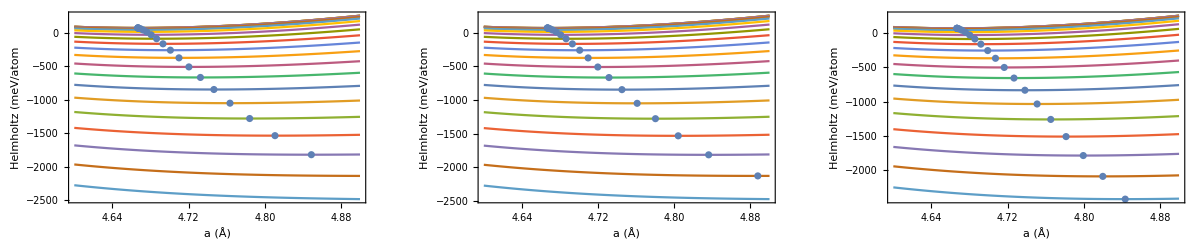

```mathematica
GraphicsGrid[{{Show[Plot[gfitPerfmode,{x,4.6,4.9},FrameLabel->{"a (Å)","Helmholtz (meV/atom"},Frame->True],ListPlot@Transpose[{minAPerfmode,mine0Perfmode}]],Show[Plot[gfitPerfmedian,{x,4.6,4.9},FrameLabel->{"a (Å)","Helmholtz (meV/atom"},Frame->True],ListPlot@Transpose[{minAPerfmedian,mine0Perfmedian}]],Show[Plot[gfitPerfhess,{x,4.6,4.9},FrameLabel->{"a (Å)","Helmholtz (meV/atom"},Frame->True],ListPlot@Transpose[{minAPerfhess,mine0Perfhess}]]}},ImageSize->1200]
```

```mathematica
Dense Minimise the free energy in volume;
```

```mathematica
(*Make a Dense list of 64 temperatures at which to do minimisation in V of F to generate G and derivative thermodynamics*)
tempsDens[t_]:=1+t^2
tlistDens=Table[tempsDens[t],{t,0,63}];
(*Fit the F(T) in V at each to make F(V;T) for each chosen trial temperature - use a polynomial basis, with up to 3rd order terms*)
gfitPerfDensmode=Table[Fit[Table[{alatts[[k]],e0Perf[[k]]+Total@fr[t,spectrumCmode[[k]],spectrumZmode[[k]],150,1,1.5]},{k,1,9}]/.t->tlistDens[[j]],{1,x,x*x,x*x*x},x],{j,1,64}];
gfitPerfDensmedian=Table[Fit[Table[{alatts[[k]],e0Perf[[k]]+Total@fr[t,spectrumCmedian[[k]],spectrumZmedian[[k]],150,1,1.5]},{k,1,9}]/.t->tlistDens[[j]],{1,x,x*x,x*x*x},x],{j,1,64}];
gfitPerfDenshess=Table[Fit[Table[{alatts[[k]],e0Perf[[k]]+Total@fr[t,spectrumChess[[k]],spectrumZhess[[k]],150,1,1.5]},{k,1,9}]/.t->tlistDens[[j]],{1,x,x*x,x*x*x},x],{j,1,64}];
```

```mathematica
Extract minimum lattice parameters and Gibbs energy at each of the dense list of  T values;
(*mode*)
minPerfDensmode=Table[Minimize[{gfitPerfDensmode[[i]],4.575<x<5},x],{i,1,64}];
minAPerfDensmode=Table[{tlistDens[[i]],minPerfDensmode[[i]][[2]][[1]][[2]]},{i,1,64}];
mine0PerfDensmode=Table[{tlistDens[[i]],minPerfDensmode[[i]][[1]]},{i,1,64}];
(*mode*)
minPerfDensmedian=Table[Minimize[{gfitPerfDensmedian[[i]],4.575<x<5},x],{i,1,64}];
minAPerfDensmedian=Table[{tlistDens[[i]],minPerfDensmedian[[i]][[2]][[1]][[2]]},{i,1,64}];
mine0PerfDensmedian=Table[{tlistDens[[i]],minPerfDensmedian[[i]][[1]]},{i,1,64}];
(*mode*)
minPerfDenshess=Table[Minimize[{gfitPerfDenshess[[i]],4.575<x<5},x],{i,1,64}];
minAPerfDenshess=Table[{tlistDens[[i]],minPerfDenshess[[i]][[2]][[1]][[2]]},{i,1,64}];
mine0PerfDenshess=Table[{tlistDens[[i]],minPerfDenshess[[i]][[1]]},{i,1,64}];
```

#### Thermal expansion;

```mathematica
minAPerfDenshess[[-1]]
minAPerfDensmedian[[-1]]
```

{3970,4.82742}

{3970,4.92024}

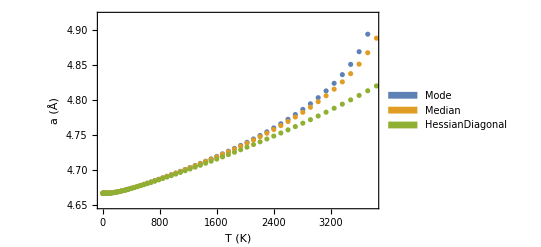

```mathematica
ListPlot[{minAPerfDensmode,minAPerfDensmedian,minAPerfDenshess},FrameLabel->{"T (K)","a (Å)"},Frame->True,PlotLegends->SwatchLegend[{"Mode","Median","HessianDiagonal"}],PlotRange->{{0,3800},{4.65,4.92}}]
```

```mathematica
Fit volume expansion to 3rd power in temperature  and get dimensionless log volume epansion;
(*Thermal expansivity - VdV/dT - http://journals.aps.org/prb/pdf/10.1103/PhysRevB.76.064116*)
(*Mode*)
minAPerfDensFitmode=Fit[minAPerfDensmode,{t^3,t^2,t,1},t]
dVdTmode[T_]=D[minAPerfDensFitmode,t]//Simplify;
VdVdTmode[T_]=(1/minAPerfDensFitmode)*D[minAPerfDensFitmode,t]//Simplify;
(*Median*)
minAPerfDensFitmedian=Fit[minAPerfDensmedian,{t^3,t^2,t,1},t]
dVdTmedian[T_]=D[minAPerfDensFitmedian,t]//Simplify;
VdVdTmedian[T_]=(1/minAPerfDensFitmedian)*D[minAPerfDensFitmedian,t]//Simplify;
(*Hessian Diagonal*)
minAPerfDensFithess=Fit[minAPerfDenshess,{t^3,t^2,t,1},t]
dVdThess[T_]=D[minAPerfDensFithess,t]//Simplify;
VdVdThess[T_]=(1/minAPerfDensFithess)*D[minAPerfDensFithess,t]//Simplify;
```

4.66003+0.0000591259 t-2.98191×10^-8 t^2+8.79636×10^-12 t^3

4.66343+0.0000348888 t-6.23151×10^-9 t^2+3.19382×10^-12 t^3

4.66502+0.0000219846 t+6.34041×10^-9 t^2-4.19535×10^-13 t^3

-100+21.4591 (4.66003+0.0000591259 t-2.98191×10^-8 t^2+8.79636×10^-12 t^3)

-100+21.4435 (4.66343+0.0000348888 t-6.23151×10^-9 t^2+3.19382×10^-12 t^3)

-100+21.4362 (4.66502+0.0000219846 t+6.34041×10^-9 t^2-4.19535×10^-13 t^3)

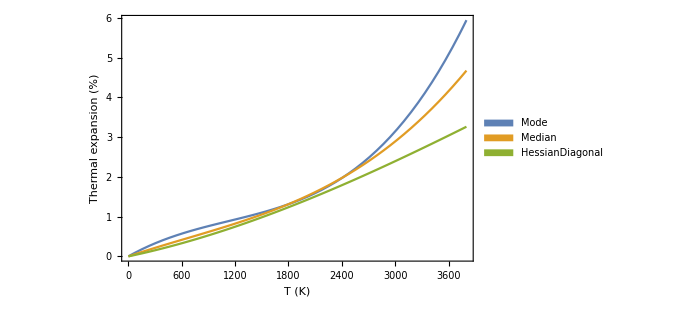

```mathematica
Plot the percent vol expansion;
percentThermalExpanMode=Evaluate[100*minAPerfDensFitmode/(Evaluate[minAPerfDensFitmode/.t->0])-100]
percentThermalExpanMedian=Evaluate[100*minAPerfDensFitmedian/(Evaluate[minAPerfDensFitmedian/.t->0])-100]
percentThermalExpanHess=Evaluate[100*minAPerfDensFithess/(Evaluate[minAPerfDensFithess/.t->0])-100]
Plot[{percentThermalExpanMode/.t->T,percentThermalExpanMedian/.t->T,percentThermalExpanHess/.t->T},{T,1,3800},FrameLabel->{"T (K)","Thermal expansion (%)"},Frame->True,ImageSize->500,PlotLegends->SwatchLegend[{"Mode","Median","HessianDiagonal"}]]
```

```mathematica
Fit the Gibbs free energy as a function of volume;
gfitPerfDensMinVmode=Table[Minimize[{gfitPerfDensmode[[i]],4.64<x<4.89},x,WorkingPrecision->20],{i,1,64}];
gfitPerfDensMinVmedian=Table[Minimize[{gfitPerfDensmedian[[i]],4.64<x<4.89},x,WorkingPrecision->20],{i,1,63}];
gfitPerfDensMinVhess=Table[Minimize[{gfitPerfDenshess[[i]],4.64<x<4.89},x,WorkingPrecision->20],{i,1,63}];
```

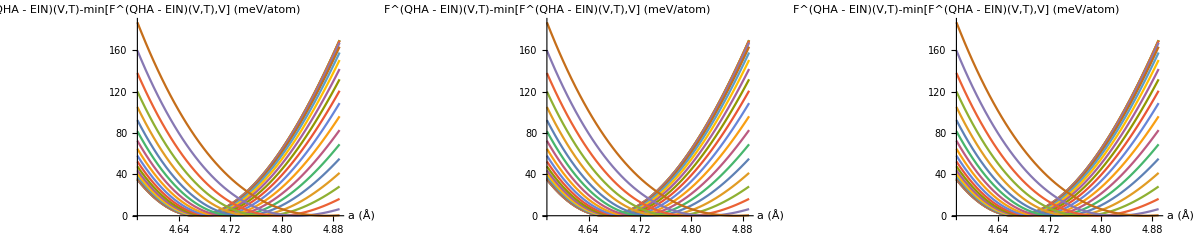

```mathematica
GraphicsGrid[{{Plot[Evaluate@Table[gfitPerfDensmode[[i]]-gfitPerfDensMinVmode[[i]][[1]],{i,1,63,3}],{x,4.575,4.89},AxesLabel->{"a (Å)","F^(QHA - EIN)(V,T)-min[F^(QHA - EIN)(V,T),V]\n (meV/atom)"}],Plot[Evaluate@Table[gfitPerfDensmode[[i]]-gfitPerfDensMinVmode[[i]][[1]],{i,1,63,3}],{x,4.575,4.89},AxesLabel->{"a (Å)","F^(QHA - EIN)(V,T)-min[F^(QHA - EIN)(V,T),V]\n (meV/atom)"}],Plot[Evaluate@Table[gfitPerfDensmode[[i]]-gfitPerfDensMinVmode[[i]][[1]],{i,1,63,3}],{x,4.575,4.89},AxesLabel->{"a (Å)","F^(QHA - EIN)(V,T)-min[F^(QHA - EIN)(V,T),V]\n (meV/atom)"}]}},ImageSize->1200]
```

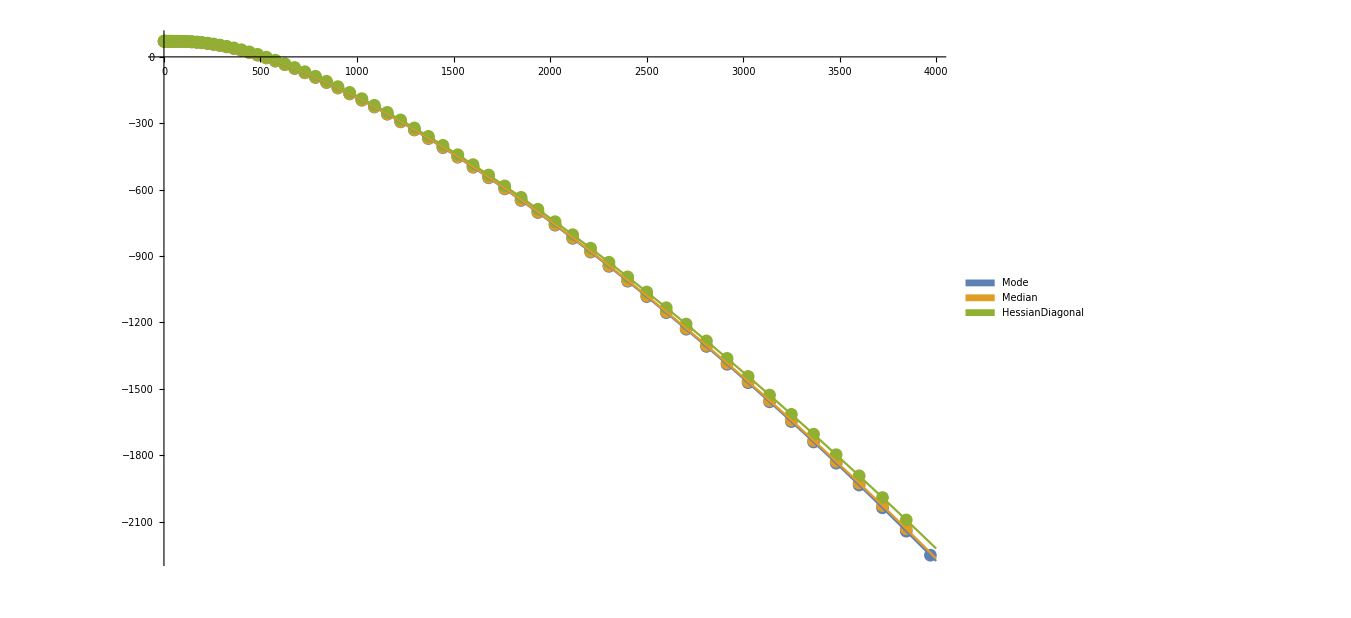

```mathematica
Gibbs free energy vs T;
gPerfTmode=Table[{tlistDens[[i]],gfitPerfDensMinVmode[[i]][[1]]},{i,1,64}];
gPerfTmedian=Table[{tlistDens[[i]],gfitPerfDensMinVmedian[[i]][[1]]},{i,1,63}];
gPerfThess=Table[{tlistDens[[i]],gfitPerfDensMinVhess[[i]][[1]]},{i,1,63}];
gPerfTintermode=Interpolation[gPerfTmode];
gPerfTintermedian=Interpolation[gPerfTmedian];
gPerfTinterhess=Interpolation[gPerfThess];
Show[ListPlot[{gPerfTmode,gPerfTmedian,gPerfThess}],Plot[{gPerfTintermode[T],gPerfTintermedian[T],gPerfTinterhess[T]},{T,1,4000},PlotLegends->SwatchLegend[{"Mode","Median","HessianDiagonal"}]],ImageSize->1000]
```

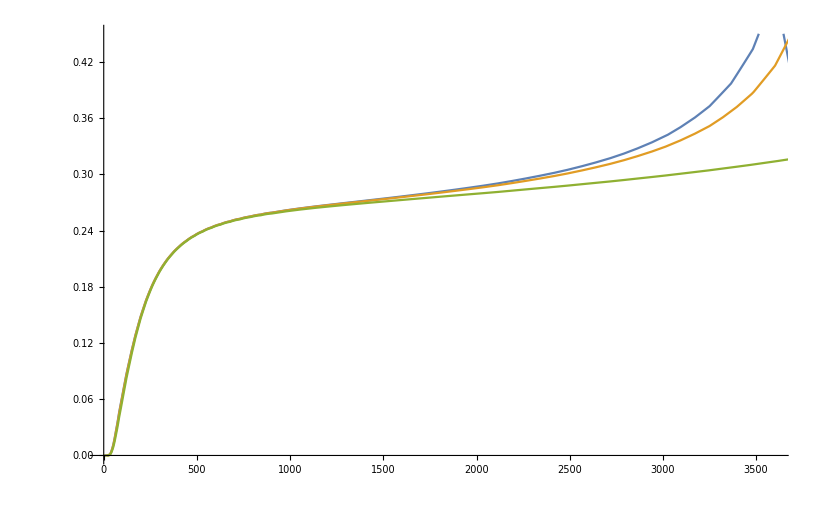

```mathematica
gPerfTCpmode=-T*D[D[gPerfTintermode[T],T],T];
gPerfTCpmedian=-T*D[D[gPerfTintermedian[T],T],T];
gPerfTCphess=-T*D[D[gPerfTinterhess[T],T],T];
Plot[{Evaluate[gPerfTCpmode],Evaluate[gPerfTCpmedian],Evaluate[gPerfTCphess]},{T,0,3700},PlotRange->{{0,3600},{0,0.45}}]
```

```mathematica
K2meV
```

0.0861733

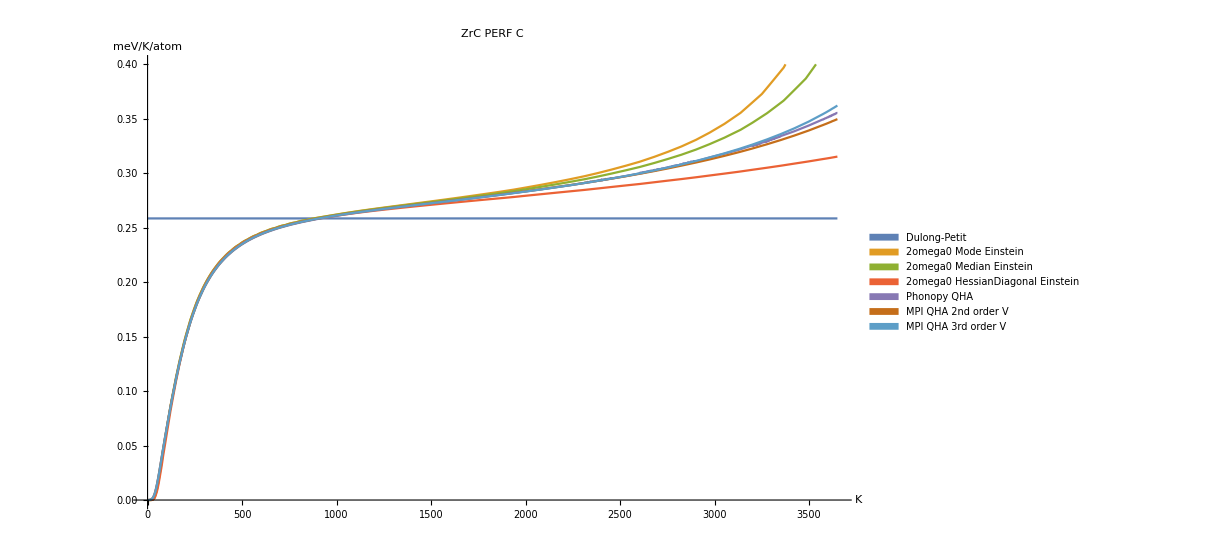

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/ZrC_QHA_output/PERF_qha700666_out/"];
(*Standard phonopy qha Cp 1K mesh*)
qhaperfCp=ReadList["Cp-temperature.dat",{Number, Number}];
qhaperfCpinter=Interpolation[Transpose[{Transpose[qhaCp][[1]],kjmol2evatom*Transpose[qhaCp][[2]]}]];
(*Standard phonopy qha Cp 2K mesh*)
(*The 2K mesh is exactly the same on average as the 1K mesh but with less instability*)
qhaperfCp2Kmesh=ReadList["2K_T_MESH/Cp-temperature.dat",{Number, Number}];
qhaperfCpinter2Kmesh=Interpolation[Transpose[{Transpose[qhaperfCp2Kmesh][[1]],kjmol2evatom*Transpose[qhaperfCp2Kmesh][[2]]}]];
(*MPI 2nd order fit PERF Cp *)
qhaperfCpMPIo2=ReadList["order2ThermoAnalyze/0_fqh/heat_capacity_isobaric",{Number, Number}];
qhaperfCpinterMPIo2=Interpolation[Transpose[{Transpose[qhaperfCpMPIo2][[1]],K2meV*Transpose[qhaperfCpMPIo2][[2]]}]];
(*MPI 2nd order fit PERF Cp *)
qhaperfCpMPIo3=ReadList["order3ThermoAnalyze/0_fqh/heat_capacity_isobaric",{Number, Number}];
qhaperfCpinterMPIo3=Interpolation[Transpose[{Transpose[qhaperfCpMPIo3][[1]],K2meV*Transpose[qhaperfCpMPIo3][[2]]}]];
(*Plot*)
Plot[{kB*3,Evaluate[gPerfTCpmode],Evaluate[gPerfTCpmedian],Evaluate[gPerfTCphess],Evaluate[qhaperfCpinter2Kmesh[T]],qhaperfCpinterMPIo2[T],qhaperfCpinterMPIo3[T]},{T,1,3650},PlotRange->{Automatic,{0,0.4}},PlotLegends->SwatchLegend[{"Dulong-Petit","2omega0 Mode Einstein","2omega0 Median Einstein","2omega0 HessianDiagonal Einstein","Phonopy QHA", "MPI QHA 2nd order V","MPI QHA 3rd order V"}],PlotLabel->"ZrC PERF C",AxesLabel->{"K","meV/K/atom"},ImageSize->900]
```